```mathematica
ShowGraphDFA[δ_,states_List,q0_,q_List]:=Graph[
MapThread[DirectedEdge,{First/@Keys[δ],Values[δ]}],
VertexSize->0.25,
VertexLabels->Placed["Name",Center],
EdgeWeight->Last/@Keys[δ],
EdgeLabels->"EdgeWeight",
VertexStyle->Join[{q0->White},Map[(#->Red)&,q]]
]
```

```mathematica
δ=Association[
{q1,"a"}->q2,
{q1, "b"}-> q3,
{q2,"a"}->q4,
{q2,"b"}->q1,
{q3,"a"}->q1,
{q3,"b"}->q4,
{q4,"a"}->q4,
{q4,"b"}->q4
];
```

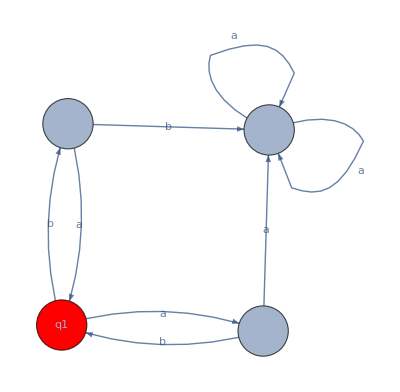

```mathematica
ShowGraphDFA[δ,{q1,q2,q3,q4},q1,{q1}]
```

Primero hay que sacar quienes van hacia 1 y como llegan a este

```mathematica
states = {q1,q2,q3,q4};
GetEntryStates[δ_, state_] := Keys[Select[δ,#==state&]]
GetFormulas[δ_, states_] := AssociationMap[GetEntryStates[δ, #]&,states];
formulas = GetFormulas[δ, states];
finalState = formulas[q1]
GetReplacement[state_, formulas_] := Switch[state,q1, state,_, formulas[state]];
expression = Map[StringRiffle[#]&,  Map[Flatten[{GetReplacement[#[[1]], formulas], #[[2]]}]&, finalState]]

StringRiffle[expression, " + "]
(*SimplifyExpression[qf_, expr_]:=Collect[ToExpression[StringRiffle[expr, " + "]],qf]; *)
SimplifyExpression[q1, expression]
expression = "ϵ + q1 ab + q1 ba";
simplifiedExpression=ToString[Collect[ToExpression[expression],q1]]
StringCases[simplifiedExpression,_~~"q1"]
StringReplace[StringCases[simplifiedExpression,__~~"q1"],  "q1"-> "*"]
```

(ab + ba) q1 + ϵ

{ q1}

StringExpression::invld: Element __ RegularExpression[(?<=q1 )] is not a valid string or pattern element in __ RegularExpression[(?<=q1 )].

StringCases[(ab + ba) q1 + ϵ,__ RegularExpression[(?<=q1 )]]

{(ab , ba) q1 , ϵ}

{{q2,b},{{{q1,b},a}}}

<|{q2,b}→q1,{q3,a}→q1|>

```mathematica
q1 = "ϵ + q2b + q3a"
```

ϵ + q2b + q3a

```mathematica
q2 = "q1*a"
```

q1*a

```mathematica
q3 = "q1*b"
```

q1*b

```mathematica
q4 = "q2*a + q4*a + q4*b"
```

q2*a + q4*a + q4*b

```mathematica
newExpression = StringReplace[q1, "q2" ->  q2]
```

ϵ + q1*ab + q3a

```mathematica
newExpression =StringReplace[newExpression, "q3" ->  q3]
```

ϵ + q1*ab + q1*ba

```mathematica
newExpression = StringReplace[newExpression, "q3" ->  q3]
```

ϵ + q1*ab + q1*ba

```mathematica
newExpression = StringReplace[newExpression, "q1*" ->  "1"]
```

ϵ + 1ab + 1ba

```mathematica
ToExpression["ϵ + q1*ab + q1*ba"]
```

ϵ + q2b + q3a ab+ϵ + q2b + q3a ba+ϵ